```mathematica
(* HNNP *)
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;

Print["Solving for RG equations..."]
SB[0]=Normal[Simplify[Part[Solve[Simplify[1/(Factor[leq[0]]*Factor[leq[1]]*Factor[leq[2]]*Factor[leq[3]]*Factor[leq[4]]*Factor[leq[5]]*Factor[leq[6]]*Factor[leq[7]])^(1/8),Assumptions->B[0]>0]==Simplify[1/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[0]],1]]];
SB[0]={B[0]-> 2 A[0]+Log[(η μ A[1]^2 A[3] A[5])/(√(η^2 μ A[1]^4+η (1+μ^2) A[1]^2 A[5]+μ A[5]^2) (η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2))^(1/4))]};
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)}
```

Solving for RG equations...

{B[0]→2 A[0]+Log[(η μ A[1]^2 A[3] A[5])/(√(η^2 μ A[1]^4+η (1+μ^2) A[1]^2 A[5]+μ A[5]^2) (η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2))^(1/4))]}

```mathematica
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}]
```

{B[0]→2 A[0]+Log[(η μ A[1]^2 A[3] A[5])/(√(η^2 μ A[1]^4+η (1+μ^2) A[1]^2 A[5]+μ A[5]^2) (η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2))^(1/4))],B[1]→(A[1] A[2] √(μ A[3]^4+η A[1]^2 A[3]^2 A[5]+η μ^2 A[1]^2 A[3]^2 A[5]+η^2 μ A[1]^4 A[5]^2))/(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2))^(1/4),B[2]→1/(√((η μ A[1]^2+A[5])/(η A[1]^2+μ A[5])) (((A[3]^2+η μ A[1]^2 A[5]) (1+η μ A[1]^2 A[3]^2 A[5]))/(μ^2 A[3]^2+η μ A[1]^2 (1+A[3]^4) A[5]+η^2 A[1]^4 A[3]^2 A[5]^2))^(1/4)),B[3]→A[3] A[4] √((η^2 μ A[1]^4+η A[1]^2 A[5]+η μ^2 A[1]^2 A[5]+μ A[5]^2)/(μ A[3]^2+η A[1]^2 A[5]+η μ^2 A[1]^2 A[3]^4 A[5]+η^2 μ A[1]^4 A[3]^2 A[5]^2)),B[4]→((A[3]^2+η μ A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]))/(√(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2))),B[5]→((η μ A[1]^2+A[5]) (μ A[3]^2+η A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]))/((η A[1]^2+μ A[5]) √(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2)))}

```mathematica
Print["Done."]
Print["Setting up RG and W matrix..."]
(* HNNP & HN3:  Sets the initial conditions. *)
(* B[0]=free energy, B[1]=backbone bond magnetization, 
   B[2]=long-range bond magnetization, B[3]=backbone coupling,
   B[4]=long-range coupling, B[5]=three-point operator *)
SIC={B[0]->0,B[1]->1,B[2]->1,B[3]->μ,B[4]->1,B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,5}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,5}];
W=Table[Factor[D[(B[i]/.SBT),A[j]]],{j,0,5},{i,0,5}];
Ω=Table[D[D[(B[i]/.SBT),A[j]],A[k]],{k,0,5},{j,0,5},{i,0,5}];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
LnZ2=FullSimplify[-2*A[0]+Log[Sum[Sum[Sum[Sum[Sum[μ^(-(x0*x3+x1*x4)/2)*η^(-(x0+x1+x2+x3+x4)/2)*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}],{x3,-1,1,2}],{x4,-1,1,2}]],Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)];
Print["Done."]

Print["Verifying integrity of RG function."]
InitRG;
Z2RGcheck=FullSimplify[LnZ2/.SAT/.η->1,Assumptions->μ>0];
InitRG;
RG;
Z1RGcheck=FullSimplify[LnZ1/.SAT/.η->1,Assumptions->μ>0];
FullSimplify[Z1RGcheck-Z2RGcheck,Assumptions->μ>0]
Print["If last output is 0, Success!!!"]
```

Done.

Setting up RG and W matrix...

Done.

Verifying integrity of RG function.

0

If last output is 0, Success!!!

Calculating the first and second derivatives of LnZ1...

Calculating all values of W/.SAT for all values of μ...

Calculating all values of Ω/.SAT for all values of μ...

μmin = 1	μmax = 10
Current μ...1....1.02...1.04...1.06...1.08...1.1...1.12...1.14...1.16...1.18...1.2...1.22...1.24...1.26...1.28...1.3...1.32...1.34...1.36...1.38...1.4...1.42...1.44...1.46...1.48...1.5...1.52...1.54...1.56...1.58...1.6...1.62...1.64...1.66...1.68...1.7...1.72...1.74...1.76...1.78...1.8...1.82...1.84...1.86...1.88...1.9...1.92...1.94...1.96...1.98...2....2.02...2.04...2.06...2.08...2.1...2.12...2.14...2.16...2.18...2.2...2.22...2.24...2.26...2.28...2.3...2.32...2.34...2.36...2.38...2.4...2.42...2.44...2.46...2.48...2.5...2.52...2.54...2.56...2.58...2.6...2.62...2.64...2.66...2.68...2.7...2.72...2.74...2.76...2.78...2.8...2.82...2.84...2.86...2.88...2.9...2.92...2.94...2.96...2.98...3....3.02...3.04...3.06...3.08...3.1...3.12...3.14...3.16...3.18...3.2...3.22...3.24...3.26...3.28...3.3...3.32...3.34...3.36...3.38...3.4...3.42...3.44...3.46...3.48...3.5...3.52...3.54...3.56...3.58...3.6...3.62...3.64...3.66...3.68...3.7...3.72...3.74...3.76...3.78...3.8...3.82...3.84...3.86...3.88...3.9...3.92...3.94...3.96...3.98...4....4.02...4.04...4.06...4.08...4.1...4.12...4.14...4.16...4.18...4.2...4.22...4.24...4.26...4.28...4.3...4.32...4.34...4.36...4.38...4.4...4.42...4.44...4.46...4.48...4.5...4.52...4.54...4.56...4.58...4.6...4.62...4.64...4.66...4.68...4.7...4.72...4.74...4.76...4.78...4.8...4.82...4.84...4.86...4.88...4.9...4.92...4.94...4.96...4.98...5....5.02...5.04...5.06...5.08...5.1...5.12...5.14...5.16...5.18...5.2...5.22...5.24...5.26...5.28...5.3...5.32...5.34...5.36...5.38...5.4...5.42...5.44...5.46...5.48...5.5...5.52...5.54...5.56...5.58...5.6...5.62...5.64...5.66...5.68...5.7...5.72...5.74...5.76...5.78...5.8...5.82...5.84...5.86...5.88...5.9...5.92...5.94...5.96...5.98...6....6.02...6.04...6.06...6.08...6.1...6.12...6.14...6.16...6.18...6.2...6.22...6.24...6.26...6.28...6.3...6.32...6.34...6.36...6.38...6.4...6.42...6.44...6.46...6.48...6.5...6.52...6.54...6.56...6.58...6.6...6.62...6.64...6.66...6.68...6.7...6.72...6.74...6.76...6.78...6.8...6.82...6.84...6.86...6.88...6.9...6.92...6.94...6.96...6.98...7....7.02...7.04...7.06...7.08...7.1...7.12...7.14...7.16...7.18...7.2...7.22...7.24...7.26...7.28...7.3...7.32...7.34...7.36...7.38...7.4...7.42...7.44...7.46...7.48...7.5...7.52...7.54...7.56...7.58...7.6...7.62...7.64...7.66...7.68...7.7...7.72...7.74...7.76...7.78...7.8...7.82...7.84...7.86...7.88...7.9...7.92...7.94...7.96...7.98...8....8.02...8.04...8.06...8.08...8.1...8.12...8.14...8.16...8.18...8.2...8.22...8.24...8.26...8.28...8.3...8.32...8.34...8.36...8.38...8.4...8.42...8.44...8.46...8.48...8.5...8.52...8.54...8.56...8.58...8.6...8.62...8.64...8.66...8.68...8.7...8.72...8.74...8.76...8.78...8.8...8.82...8.84...8.86...8.88...8.9...8.92...8.94...8.96...8.98...9....9.02...9.04...9.06...9.08...9.1...9.12...9.14...9.16...9.18...9.2...9.22...9.24...9.26...9.28...9.3...9.32...9.34...9.36...9.38...9.4...9.42...9.44...9.46...9.48...9.5...9.52...9.54...9.56...9.58...9.6...9.62...9.64...9.66...9.68...9.7...9.72...9.74...9.76...9.78...9.8...9.82...9.84...9.86...9.88...9.9...9.92...9.94...9.96...9.98...10.

Calculating all values of Υ for all values of μ...

Calculating all values of Λ for all values of μ...

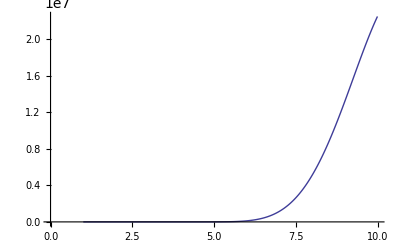

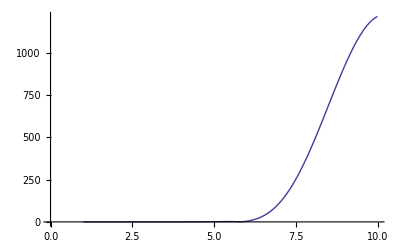

Done.

```mathematica
(*********************************)
(* 
d^2/(d Subscript[(Subscript[A, 0]), b] d Subscript[(Subscript[A, 0]), a]){LnZ^(k)(Subscript[A, 0])} = {(d LnZ1)/(d Subscript[A, α])(Subscript[A, k-1])}Subscript[Λ, α,a,b]^(k-1)+{(d^2 LnZ1)/(Subscript[dA, α] dAβ)(Subscript[A, k-1])}Subscript[Υ, β,b]^(k-1)Subscript[Υ, α,a]^(k-1)
*)


(* Sets the range of μ *)
min=1;
max=10;
inc = 0.02;
μVector=Range[min,max,inc];

(* Sets the number of RG rescalings *)
k=12;
η=1;

(*********************************)
(*
Calculates the values, {(d LnZ1)/(d Subscript[A, α])(Subscript[A, k-1])} and {(d^2 LnZ1)/(Subscript[dA, α] dAβ)(Subscript[A, k-1])}.
*)

LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,5}];
DDLnZ1 = Table[Factor[D[D[LnZ1,A[i]],A[j]]],{j,0,5},{i,0,5}];

Print["Calculating the first and second derivatives of LnZ1..."]

(*
   This routine calculates the 1st and 2nd derivatives of 
  LnZ1 for all values of μ and stores them in the variables
  DLnZ1 and DDLnZ1 respectively.
*)
DLnZ1total={};
DDLnZ1total={};
Do[
InitRG;
For[i=k,i≥0,--i,
FullSimplify[RG,Assumptions->μ>0];
];
{AppendTo[DDLnZ1total,DDLnZ1/.SAT],AppendTo[DLnZ1total,DLnZ1/.SAT]},
{μ,min,max,inc}];
(************************** END OF ROUTINE ********************************)


(* 
   This routine calculates and stores all the values
 of W/.SAT for all values of μ in the variable Wtotal. 
These values are used to calculate the Λ and Υ.
*)
Print["Calculating all values of W/.SAT for all values of μ..."];
Wtotal={};
Do[
InitRG;                                            (* initialize RG for each μ *)
Witer={};                                     (* reset the Witer list that will hold each W/.SAT value *)
AppendTo[Witer,W/.SAT];    (* first element in the Witer list when no RG has occured *)

For[i=k,i≥0,--i,
RG;
AppendTo[Witer,W/.SAT];  (* after RG, append W/.SAT to Witer. this is the equivalent of W^l in write-up *)
];
AppendTo[Wtotal,Witer],      (* the values stored in Witer are pushed to the Wtotal list *)
{μ,min,max,inc}                       (* Do loop goes from min to max in increments of inc *)
];
(* end of Do loop *)
(************************** END OF ROUTINE ********************************)

(* 
   This routine calculates and stores all the values
 of Ω/.SAT for all values of μ in the variable Ωtotal. 
These values are used to calculate the Λ and Υ.
*)
Print["Calculating all values of Ω/.SAT for all values of μ..."];
WriteString["stdout","μmin = ",min,"\tμmax = ",max,"\nCurrent μ"];
Ωtotal={};
Do[
InitRG;                                            (* initialize RG for each μ *)
Ωiter={};                                     (* reset the Ωiter list that will hold each Ω/.SAT value *)
AppendTo[Ωiter,Ω/.SAT];    (* first element in the Ωiter list when no RG has occured *)

For[i=k,i≥0,--i,
RG;
AppendTo[Ωiter,Ω/.SAT];  (* after RG, append Ω/.SAT to Ωiter. this is the equivalent of Ω^l in write-up *)
];
AppendTo[Ωtotal,Ωiter]; (* the values stored in Ωiter are pushed to the Ωtotal list *)
WriteString["stdout","...",μ],
{μ,min,max,inc}                       (* Do loop goes from min to max in increments of inc *)
];
(* end of Do loop *)
(************************** END OF ROUTINE ********************************)


(*
	This routine calculates and stores all values for Υ
   for all values of μ in the variable Υtotal. These are 
   needed to calculate Λ.
*)
Print["Calculating all values of Υ for all values of μ..."];
(* This list will hold all values of Υ for all values of μ.*)
Υtotal={}; 

(* total number of index values of μ *)
μindexMax=Ceiling[(max-min)/inc];
WindexMax=Part[Dimensions[Wtotal],2];

For[μindex=1,μindex≤μindexMax,++μindex,
(* Creates new list in which values of Υ will be stored *)
Υiter={};

(* Initially, Υ0 = W0 and is appended to the first element of Υtotal. *)
Υcurrent=Part[Part[Wtotal,μindex],1];
AppendTo[Υiter,Υcurrent];

(* This For loop calculates values of W^l.Υ^(l-1) and inserts them into the Υiter list. *)
For[Windex=2,Windex≤WindexMax,++Windex,
Υcurrent=(Part[Part[Wtotal,μindex],Windex]).Υcurrent;
AppendTo[Υiter,Υcurrent];
];

(* Υiter list for current μindex value is inserted into Υtotal list. *)
AppendTo[Υtotal,Υiter];
];
(************************** END OF ROUTINE ********************************)

(*
	This routine calculates Λ for all values of μ 
   in the variable Λtotal. 
*)
Print["Calculating all values of Λ for all values of μ..."];
Λtotal={};
ΛindexMax=Part[Dimensions[Part[Ωtotal,1]],1];
For[μindex=1,μindex≤μindexMax,++μindex,
Λcurrent=Part[Part[Ωtotal,μindex],1];
For[Λindex=2,Λindex≤ΛindexMax,++Λindex,
Λcurrent=((Part[Part[Wtotal,μindex],Λindex]).(Λcurrent)) + ((Part[Part[Ωtotal,μindex],Λindex]).(Part[Part[Υtotal,μindex],(Λindex-1)]).(Part[Part[Υtotal,μindex],(Λindex-1)]));
];
AppendTo[Λtotal,Λcurrent];
];
(************************** END OF ROUTINE ********************************)


(* Final calculation for susceptibility *)
DDLnZk={};
For[μindex=1,μindex≤μindexMax,++μindex,
DDLnZkTemp=((Part[DLnZ1total,μindex]).(Part[Λtotal,μindex]))+((Part[DDLnZ1total,μindex]).(Part[Part[Υtotal,μindex],WindexMax]).(Part[Part[Υtotal,μindex],WindexMax]));
AppendTo[DDLnZk,DDLnZkTemp];
];

(* 
	Splits the result into parts and stores them in PartX. Note that 
   1,1; 2,2; ...6,6 refer to second derivates with respect to the same
   variable. For instance, Part[Part[...4],4]
   would be d^2/Subscript[dH, s]^2.
*)
Part1={};
Part2={};
Part3={};
Part4={};
Part5={};
Part6={};
For[μindex=1,μindex≤μindexMax,++μindex,
AppendTo[Part1,Part[Part[Part[DDLnZk,μindex],1],1]];
AppendTo[Part2,Part[Part[Part[DDLnZk,μindex],2],2]];
AppendTo[Part3,Part[Part[Part[DDLnZk,μindex],3],3]];
AppendTo[Part4,Part[Part[Part[DDLnZk,μindex],4],4]];
AppendTo[Part5,Part[Part[Part[DDLnZk,μindex],5],5]];
AppendTo[Part6,Part[Part[Part[DDLnZk,μindex],6],6]];
];

(* Plots the spin and bond susceptibilities respectively. *)
ListLinePlot[Partition[Riffle[μVector,Part4],2]]
ListLinePlot[Partition[Riffle[μVector,Abs[Part5]],2]]

Print["Done."]
```

```mathematica
Simplify[Factor[req[0]]*Factor[req[1]]*Factor[req[2]]*Factor[req[3]]*Factor[req[4]]*Factor[req[5]]*Factor[req[6]]*Factor[req[7]]]
```

(ⅇ^(-16 A[0]) (μ A[1]^2+A[5])^4 (A[1]^2+μ A[5])^4 (μ A[3]^2+A[1]^2 A[5])^2 (A[3]^2+μ A[1]^2 A[5])^2 (μ+A[1]^2 A[3]^2 A[5])^2 (1+μ A[1]^2 A[3]^2 A[5])^2)/(μ^8 A[1]^16 A[3]^8 A[5]^8)

```mathematica
(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])
```

ⅇ^(-8 B[0])

```mathematica
Solve[Log[1/(μ^1 A[1]^2 A[3]^1 A[5]^1)ⅇ^(-2A[0]) (μ A[1]^2+A[5])^(1/2) (A[1]^2+μ A[5])^(1/2) (μ A[3]^2+A[1]^2 A[5])^(1/4) (A[3]^2+μ A[1]^2 A[5])^(1/4) (μ+A[1]^2 A[3]^2 A[5])^(1/4) (1+μ A[1]^2 A[3]^2 A[5])^(1/4)]==-B[0],B[0]]
```

{{B[0]→-Log[1/(μ A[1]^2 A[3] A[5])ⅇ^(-2 A[0]) √(μ A[1]^2+A[5]) √(A[1]^2+μ A[5]) (μ A[3]^2+A[1]^2 A[5])^(1/4) (A[3]^2+μ A[1]^2 A[5])^(1/4) (μ+A[1]^2 A[3]^2 A[5])^(1/4) (1+μ A[1]^2 A[3]^2 A[5])^(1/4)]}}

```mathematica
{B[0]->Log[(ⅇ^(2 A[0]) μ A[1]^2 A[3] A[5])/(√(μ A[1]^2+A[5]) √(A[1]^2+μ A[5]) (μ A[3]^2+A[1]^2 A[5])^(1/4) (A[3]^2+μ A[1]^2 A[5])^(1/4) (μ+A[1]^2 A[3]^2 A[5])^(1/4) (1+μ A[1]^2 A[3]^2 A[5])^(1/4))]}
```

```mathematica
SB[0]={B[0]->Log[(ⅇ^(2 A[0]) μ A[1]^2 A[3] A[5])/(√(μ A[1]^2+A[5]) √(A[1]^2+μ A[5]) (μ A[3]^2+A[1]^2 A[5])^(1/4) (A[3]^2+μ A[1]^2 A[5])^(1/4) (μ+A[1]^2 A[3]^2 A[5])^(1/4) (1+μ A[1]^2 A[3]^2 A[5])^(1/4))]};
```

```mathematica
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)}
```

{B[0]→2 A[0]+Log[(μ A[1]^2 A[3] A[5])/(√(μ A[1]^2+A[5]) √(A[1]^2+μ A[5]) (μ A[3]^2+A[1]^2 A[5])^(1/4) (A[3]^2+μ A[1]^2 A[5])^(1/4) (μ+A[1]^2 A[3]^2 A[5])^(1/4) (1+μ A[1]^2 A[3]^2 A[5])^(1/4))]}